## Desempenho médio de algoritmos com integrais

Aluno: Pedro Sobota

Na computação, temos o conceito de tempo de execução de um algoritmo. O tempo corresponde a quanto tempo o algoritmo leva para executar suas instruções sobre um conjunto de entradas e retornar um resultado.

Uma forma de medir o desempenho de um algoritmo é estipular sua performance em função do tamanho do conjunto de entradas, ou seja, quantos elementos há em um vetor que o algoritmo deve percorrer, por exemplo.

Vamos verificar dois exemplos de algoritmos que percorrem um vetor.

```mathematica
(*
Algoritmo 1.
calcula a média de valores da lista.
para cada item na lista:
    soma o valor do item à média.
*)
```

```mathematica
(*
Algoritmo 2.
para cada item na lista:
    calcula a média de valores da lista.
    soma o valor do item à média.
*)
```

O primeiro algoritmo calcula a média uma vez apenas, no início do procedimento.
O segundo algoritmo calcula a média novamente todas as vezes que encontra um novo elemento para analisar.

Como calcular a média implica percorrer todos os elementos, o algoritmo 1 terá um desempenho linear pois ele percorre o vetor uma vez para calcular a média e uma vez mais para somar cada valor de elementos.
A quantidade de vezes que irá percorrer o vetor será 1+n, sendo n a quantidade de elementos.

Já o algoritmo 2 terá um desempenho exponencial pois ele percorre o vetor duas vezes a cada elemento, uma para calcular a média, outra para somar o valor do elemento.
A quantidade de vezes que irá percorrer o vetor será n^2+n, sendo n a quantidade de elementos.

Com estas características estipuladas, podemos considerar funções de desempenho do algoritmo e obter os gráficos. Vamos tomar como exemplo dois algoritmos fictícios, um de desempenho quadrático e um linear em 8x:

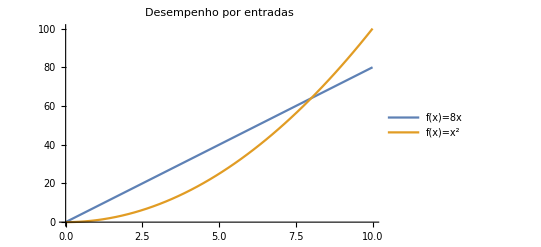

```mathematica
Plot[{8x,x^2},{x,0,10},PlotLegends->{"f(x)=8x","f(x)=x^2"},PlotLabel->"Desempenho por entradas",Frame->False,FrameLabel->{"n","a"},PlotTheme->"Default"(*,Epilog->{InfiniteLine[{{0,400/10},{10,400/10}}],InfiniteLine[{{0,333/10},{10,333/10}}]}*)]
```

Em cada ponto da abscissa, podemos obter um valor da ordenada para o desempenho daquele algoritmo para aquele n.

Porém, vamos supor que não temos uma previsão exata de quantos elementos de entrada o vetor possuirá. Para comparar o desempenho dos algoritmos neste cenário, podemos buscar uma “média” do desempenho do algoritmo em uma faixa de valores de n e comparar as médias. Isto significaria que o algoritmo tem um desempenho melhor ou pior em média dentro do intervalo.

Para obter a média, podemos tomar a integral:

∫8x=8∫x=8 x^2/2=4 x^2 e 
∫x^2=x^3/3.

Obtendo assim as integrais indefinidas das funções desempenho. Com as integrais indefinidas, podemos estipular o intervalo de n e obter as integrais definidas:

n=10
∫_0^n 8x=4·10^2-4·0^2=400 e
∫_0^n x^2=10^3/3-0^3/3=333,OverBar[3].

Agora, apenas comparando os valores das integrais definidas, podemos observar qual algoritmo tem desempenho médio superior (o algoritmo quadrático, com x̄=333. OverBar[3]), dado um intervalo específico de possibilidades de tamanhos de entrada.

Finalmente, para obter uma avaliação da variação da média ao longo de diferentes intervalos, podemos comparar a média, ou seja, a integral definida, em função dos limites superiores dos intervalos.

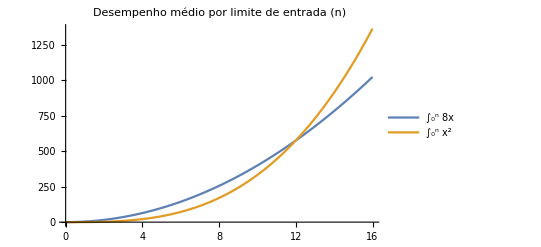

```mathematica
Plot[{4#^2&[x],#^3/3&[x]},{x,0,16},PlotLabel->"Desempenho médio por limite de entrada (n)",PlotLegends->{"∫_0^n 8x","∫_0^n x^2"}]
```

Enquanto o primeiro gráfico fornece um resultado para valores de entrada específicos, o segundo gráfico pode nos fornecer a comparação quando temos incerteza quanto ao limite inferior das entradas, mas podemos estimar um limite superior.

Neste, vemos que o algoritmo quadrático tem performance média superior para qualquer tamanho de entrada até aproximadamente 12, quando o algoritmo linear passa a ser vantajoso.